```mathematica
SetDirectory[NotebookDirectory[]];
<<RLBotIO`
<<RLBotMisc`
```

```mathematica
defaultCar
```

<|time→0,pos→{0,0,0},vel→{0,0,0},euler→{0,0,0},θ→{{1,0,0},{0,1,0},{0,0,1}},ω→{0,0,0},sup→0,jump→0,dblj→0,grnd→1,boost→0,κ→0.,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>

```mathematica
getRPY[ω0_, ωT_, J_, θ_, Δt_] := Module[{
Ω0 = Transpose[θ].ω0, 
ΩT= Transpose[θ].ωT,
T = AirTorque,
H = AirDamping,
a,b,c
},

a = Table[Δt/J T[[i]], {i, 1, 3}];
b = Table[ -Δt/J H[[i]] Ω0[[i]], {i, 1, 3}];b[[1]] = 0;
c = Table[ΩT[[i]]-(1 + Δt/J H[[i]])Ω0[[i]], {i, 1, 3}];

Table[solvePWL[a[[i]], b[[i]], c[[i]]], {i, 1, 3}]

]

ωNext[ω0_, rpy_, J_, θ_, Δt_] := Module[
{T, H, τ, ω},
T = DiagonalMatrix[AirTorque];
H = DiagonalMatrix[AirDamping * {1,(1-Abs[rpy[[2]]]), (1-Abs[rpy[[3]]])}];
τ = θ.(T.rpy+H.Transpose[θ].ω0);
ω = ω0 + τ/J Δt ;
ω *= Min[1.0, ωMaxAerial/Norm[ω]];
ω
]

ωTarget[θ0_, θ1_, {ω0x_, ω0y_, ω0z_}, T_, τ_] := Module[{
ωAvg = rotationAxis[θ1.Transpose[θ0]],
A, b
},
If[T < τ,
A = {{T^2/(2 τ),(T^3 ω0z)/(12 τ),-(T^3 ω0y)/(12 τ)},{-(T^3 ω0z)/(12 τ),T^2/(2 τ),(T^3 ω0x)/(12 τ)},{(T^3 ω0y)/(12 τ),-(T^3 ω0x)/(12 τ),T^2/(2 τ)}};
b = ωAvg-{T ω0x-(T^2 ω0x)/(2 τ),T ω0y-(T^2 ω0y)/(2 τ),T ω0z-(T^2 ω0z)/(2 τ)};
,
A = {{T-τ/2,(T^2 ω0z)/12,-(T^2 ω0y)/12},{-(T^2 ω0z)/12,T-τ/2,(T^2 ω0x)/12},{(T^2 ω0y)/12,-(T^2 ω0x)/12,T-τ/2}};
b = ωAvg-{(τ ω0x)/2,(τ ω0y)/2,(τ ω0z)/2};
];
LinearSolve[A, b]
]
```

```mathematica
drawPlots[range_] := {which = "pos";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ImageSize->Large
],

which = "vel";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ImageSize->Large
],

which = "ω";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Norm[#[which]]& /@ predictions[[range]], PlotStyle->{Dashed, Red},PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ListLinePlot[Norm[#[which]]& /@ car[[range]], PlotStyle->Red,PlotRange->All],
PlotRange->All,
ImageSize->Large
]}
```

```mathematica
g = -651.47;
boostAccel = 1060.0;
timeLimit = 0.3;
ωMaxAerial= 5.5;
drivingSpeed = 1450;
brakingForce = 3500;
coastingForce = 525;
throttleThreshold = 0.05;
throttleForce = 1550;
maxSpeed = 2275;
minSpeed = 10;


carMass = 180.0;
carInertiaMoment =10.5;
dodgeLimit = 1.25;
jumpMax = 0.2;
jumpImpulse = 52500;
jumpForce = 262500;
liftoffTime = 0.045;
throttleForce = 12000;
boostForce = 178500;
AirTorque = {-400.0, -130.0, 95.0};
AirDamping  = {-50.0, -30.0, -20.0};

κ[x_]:= Interpolation[({{0, 0.0069}, {500, 0.00398}, {1000, 0.00235}, {1500, 0.001375}, {1750, 0.0011}, {2500, 0.0008}}), InterpolationOrder->1][x]

ϕ[x_] := Interpolation[({{0, 29.9238}, {500, 18.0187}, {1000, 10.3292}, {1500, 6.0199}, {1750, 4.8504}, {3000, 1.9751}}), InterpolationOrder->1][x]

AirDodge[state_, input_, Δt_] := Module[{
next = state

},
(* TODO *)
next
]

drivingForceForward[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"],
turnDamping
},
turnDamping = (-0.07186693033945346 Abs[steering]-0.055453237281917644  Abs[ωu]+0.0006255296371672214 Abs[vl]) vf;
If[boost == 1,

(* boosting *)
If[vf < 0,
brakingForce,
If[0 <vf <drivingSpeed,
(maxSpeed - Abs[vf]),
If[vf > maxSpeed,
98.25785130764065 Abs[ωu],
boostAccel +turnDamping
]
]
],

(* not boosting *)
If[throttle * Sign[vf] > -0.001 && Abs[vf] > minSpeed, 
If[Abs[throttle] <  throttleThreshold && Abs[vf] > minSpeed,
-coastingForce Sign[vf] + turnDamping,
If[Abs[vf]>drivingSpeed,
turnDamping,
throttle(1550 - Abs[vf]) + turnDamping
]
],
brakingForce Sign[throttle]
]
]
]

drivingForceLeft[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"]
},
 (1380.4531378064655 steering+7.82811881088291 throttle-15.006402973550104 vl+668.1208332047357 ωu)(1-Exp[-0.0011607974131331873 Abs[vf]])
]

drivingTorqueUp[state_, input_] := Module[{
steering=input["steer"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"]
},
15(steering κ[Abs[vf]]vf- ωu)
]

AirDodge[state_, input_, Δt_] := Module[{},
state
]

Jump[state_, input_, Δt_] := Module[{
next=state,
θ=state["θ"],
a = 0,
forward, left, up
},
{forward, left, up} = Transpose[θ];
If[state["jump"] == 0, 
next["jump"] = 1;
next["jumpTimer"] = 0;
,
If[state["grnd"] == 1,
a += g up;
];
If[state["jumpTimer"] == 0,
a+=1/Δt jumpImpulse/carMass up;
];
If[state["jumpTimer"] < jumpMax,
a+=jumpForce/carMass up;
];
If[state["jumpTimer"] > liftoffTime,
next["grnd"] = 0
];
next["jumpTimer"]+=Δt;
next["accel"]+=a;
next["vel"]+=a Δt;
next["pos"]+=a Δt^2;
];
next
]

GroundControl[state_, input_, Δt_] := Module[{
next = state,
forward=(state["θ"][[All, 1]]),
left=(state["θ"][[All, 2]]),
up=(state["θ"][[All, 3]]),
Fforward,Fleft,Tup
},
Fforward=drivingForceForward[state, input];
Fleft=drivingForceLeft[state, input];
Tup=drivingTorqueUp[state, input];
next["vel"]=state["vel"] + {1,1,0}*(Fforward*forward + Fleft*left) Δt;
next["pos"]=state["pos"] + next["vel"]Δt;
next["ω"]= {0.9, 0.9, 1.0}*state["ω"] + Tup*up Δt;
next["θ"]=RotationMatrix[next["ω"].up Δt, up].state["θ"];
next
]

AerialControl[state_, input_, Δt_] := Module[{
next = state,
θ = state["θ"],
rpy = {input["roll"], input["pitch"], input["yaw"]},
ωAvg, ωLocal, T, H, 
forward, left, up
},
{forward, left, up} = Transpose[θ];
next["time"] += Δt;
next["accel"] = {0, 0, g};
next["accel"]+=forward/carMass(input["boost"](boostForce + throttleForce));
next["accel"]+=forward/carMass((1 - input["boost"]) input["thr"] throttleForce);
next["vel"]=state["vel"] + next["accel"] Δt;
next["pos"]=state["pos"] + next["vel"] Δt; 
T = DiagonalMatrix[AirTorque];
H = DiagonalMatrix[AirDamping * {1,(1-Abs[rpy[[2]]]), (1-Abs[rpy[[3]]])}];
next["torque"] = θ.(T.rpy+ H.Transpose[θ].state["ω"]);
next["ω"] = state["ω"] + next["torque"]/carInertiaMoment Δt ;
ωAvg = 1/2(state["ω"] +next["ω"]);
next["θ"] = RotationMatrix[Norm[ωAvg]Δt,Normalize[ωAvg]].θ;
next["ω"] *= Min[1.0, ωMaxAerial/Norm[next["ω"]]];
next["vel"] *= Min[1.0, maxSpeed/Norm[next["vel"]]];
next
]

CarControl[state_, input_, Δt_] := Module[{next},
next = If[state["grnd"] == 0,
AerialControl[state, input, Δt],
GroundControl[state, input, Δt]
];
If[input["jump"] == 1,
next = If[state["dblj"] == 0,
Jump[next, input, Δt],
AirDodge[next, input, Δt]
];
];
next
]
```

```mathematica
simulate[substeps_, delay_, car_, inputs_] := Module[{
predictions,lastPrediction,Δt
},
predictions = Table[car[[i]], {i, 1, delay}];
lastPrediction = predictions[[-1]];
Do[
Δt = car[[delay + i + 1]]["time"] - car[[delay + i]]["time"];
Do[
lastPrediction = CarControl[lastPrediction, inputs[[i]],  Δt/substeps],
{j, 1, substeps}
];
AppendTo[predictions,lastPrediction];
,
{i, 1, Length[car]-delay-1}
];
predictions
]
```

```mathematica
rawcar[[1]]
```

<|time→1.69105,pos→{0.,-4608.,16.9413},vel→{0.,0.011285,9.7853},euler→{-101,16384,0},θ→{{6.12295×10^-17,-1.,5.92919×10^-19},{0.999953,6.12323×10^-17,0.0096831},{-0.0096831,0.,0.999953}},ω→{0.001774,0.,0.},sup→0,jump→0,dblj→0,grnd→1,boost→100,κ→0.,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>

```mathematica
{rawcar, rawinputs} = ImportEpisode[NotebookDirectory[] <> "aerial_120hz.txt"]
```

{{<|time→1.69105,pos→{0.,-4608.,16.9413},vel→{0.,0.011285,9.7853},euler→{-101,16384,0},8,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>,<|1|>,7704,<|1|>,<|time→71.8042,pos→{-2374.49,-3092.14,17.01},vel→{0.,0.,8.32},10,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>},1}
 |  |  |  |

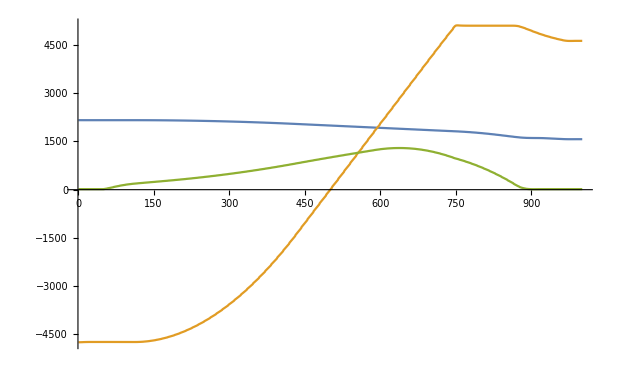

```mathematica
range =4000;;5000;
car = rawcar[[range]];
inputs = rawinputs[[range]];
ListLinePlot[Transpose[#["pos"] & /@ car]]
```

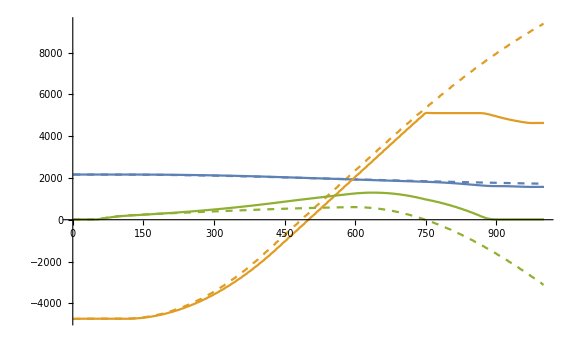
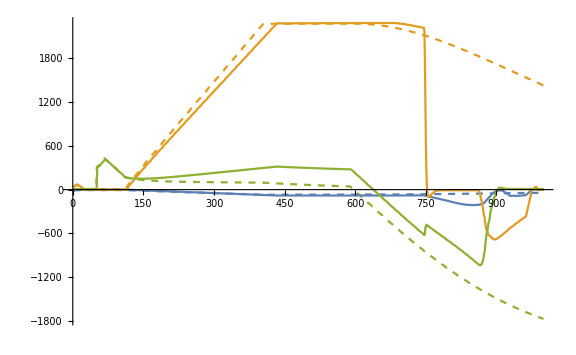
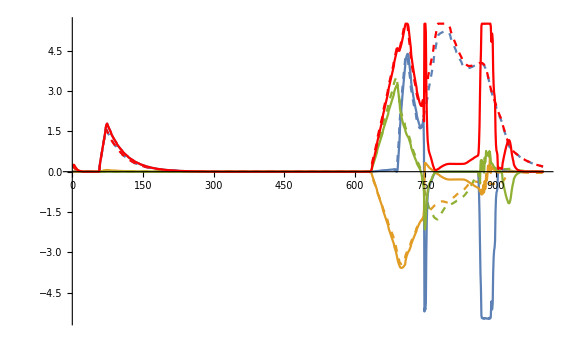

```mathematica
delay = 1;
substeps = 1;
predictions = simulate[substeps, delay, car, inputs];
drawPlots[1;;-1]
```

```mathematica
car[[300]]
```

<|time→64.9126,pos→{-1929.11,2367.41,1363.35},vel→{-1651.08,1574.54,291.053},θ→{{-0.34419,0.345778,0.872909},{-0.164003,-0.937563,0.306722},{0.924465,-0.0375888,0.379408}},ω→{-2.6218,2.04357,4.38163},sup→1,jump→1,dblj→0,grnd→0,boost→100,κ→0.,wheelAngle→0.,jumpTimer→0.,torque→{0.,0.,0.},accel→{0.,0.,0.}|>

```mathematica
car[[300]]["euler"] π/32768.0
```

{0.752034,1.60694,0.00268447}

```mathematica
θ = car[[300]]["θ"]
```

{{-0.0263906,-0.99941,0.022003},{0.729824,-0.0343038,-0.682774},{0.683126,-0.00196047,0.730298}}

```mathematica
Transpose[θ].carVel
```

{1143.23,0.530159,-755.875}

```mathematica
carVel = car[[300]]["vel"]
```

{-47.3318,1350.43,228.953}

```mathematica
carPos = car[[300]]["pos"]
```

{2121.97,-3568.89,490.264}

```mathematica
ballPos = {0, 0, 100}
```

{0,0,100}

```mathematica
Transpose[θ].(ballPos - carPos)
```

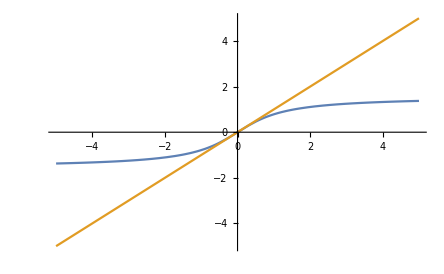

```mathematica
Plot[{ArcTan[x], x}, {x, -5, 5}]
```

```mathematica
carPos = car[[300]]["pos"]
```

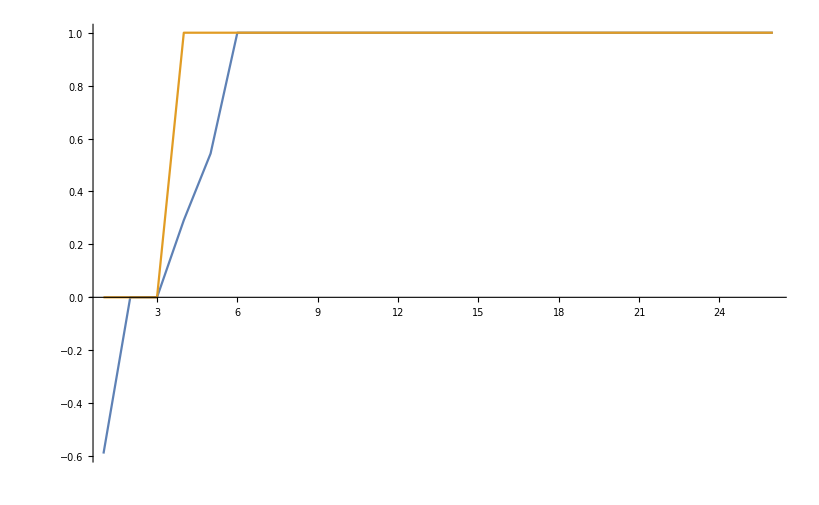

```mathematica
ListLinePlot[{
#["steer"] & /@ inputs[[50;;75]],
#["jump"] & /@ inputs[[50;;75]]
}, PlotRange->All]
```

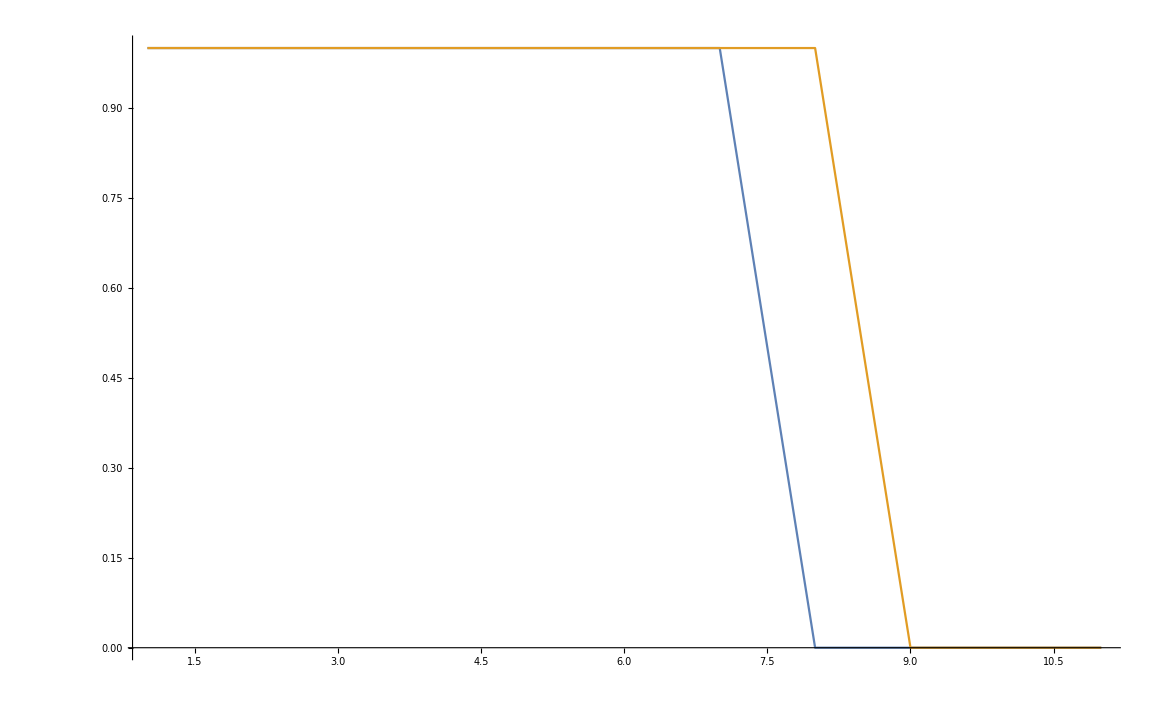

```mathematica
ListLinePlot[{
#["grnd"] & /@ car[[50;;60]],
#["grnd"] & /@ predictions[[50;;60]]
}, PlotRange->All]
```

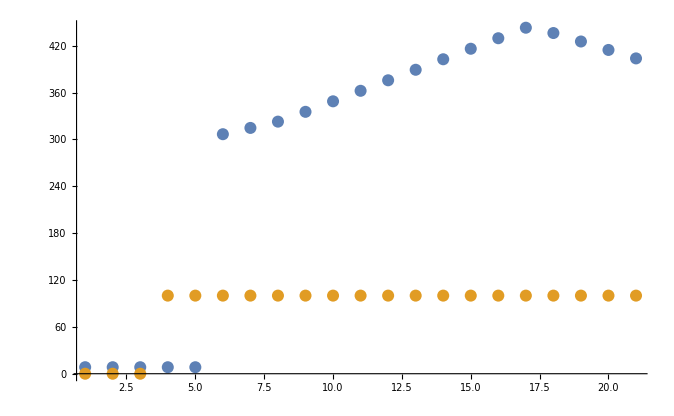

```mathematica
ListPlot[{
#["vel"][[3]] & /@ car[[50;;70]],
100#["jump"] & /@ inputs[[50;;70]]
}, PlotRange->All]
```

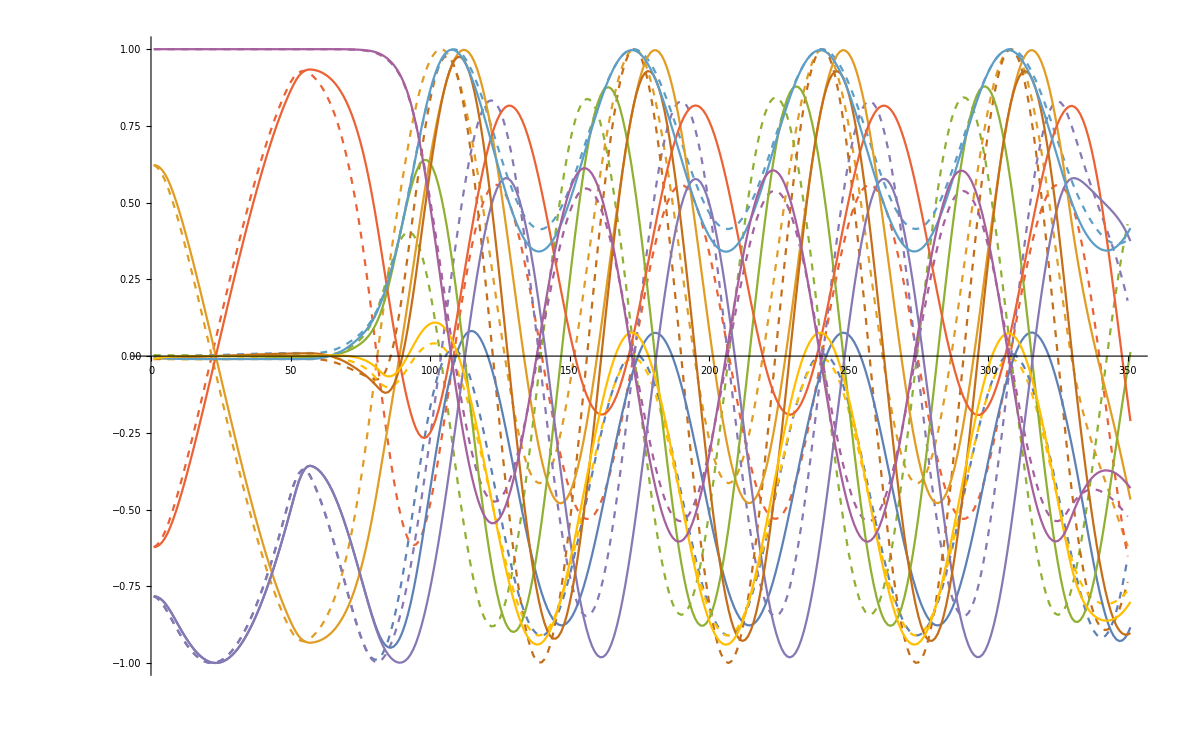

```mathematica
Show[
ListLinePlot[Transpose[Flatten[#["θ"]] & /@ predictions], PlotStyle->Dashed],
ListLinePlot[Transpose[Flatten[#["θ"]] & /@ car]]
]
```

```mathematica
n = 60;
ω0 = RandomReal[{-1, 1}, 3];
θ0 = Orthogonalize[RandomReal[{-1, 1}, {3,3}]];
θ0 *= Det[θ0];
θ1 = Orthogonalize[RandomReal[{-1, 1}, {3,3}]];
θ1 *= Det[θ1];
car = generateCar[ω0, θ0, 1.0/60.0, n];
α = 0.01;
ϵ = 0.01;
{r, p, y, τ} = {0.0, 0.0, 0.0, 0.5};
eye = IdentityMatrix[4];
AngleBetween[simulate[1, 1, car, generateInputs[{0, 0, 0,0.5}, n]][[-1]]["θ"], θ1]
```

1.6798

```mathematica
α = 0.001;
```

```mathematica
pred = simulate[1, 1, car, generateInputs[{r,p,y,τ}, n]];
```

```mathematica
Do[
F=AngleBetween[simulate[1, 1, car, generateInputs[{r,p,y,τ}, n]][[-1]]["θ"], θ1];
δF = Table[
AngleBetween[simulate[1, 1, car, generateInputs[Clamp /@  ({r,p,y,τ} + ϵ eye[[i]]), n]][[-1]]["θ"], θ1],
{i, 1, 4}
];
gradF = (δF - F)/ϵ;
{r, p, y, τ}= Clamp /@ ({r, p, y, τ} - α gradF);
Print[F];
,
{j, 1, 15}
]
```

0.0839624

0.0756971

0.0676039

0.0597469

0.0522186

0.0451527

0.0387369

0.0332095

0.0288012

0.0256117

0.0235198

0.022249

0.0215117

0.0210919

0.0208529

```mathematica
iterationsToConverge[ω0_, ωT_] :=Module[{ω = ω0, count = 0},
Do[
ω = ωNext[ω, getRPY[ω, ωT, J, θ, Δt], J, θ, Δt];
count++;
If[Norm[ω - ωT] < 0.001, Break[]];
,
{i, 1, 1000}
];
count
]
```

```mathematica
Δt = 0.001;
```

```mathematica
Histogram3D[iters]
```

-Graphics3D-

```mathematica
controller[ω0_, ωTarget_, θ0_, θTarget_, nsteps_, Δt_, τ_, noinput_] := Module[{state, input, history, ωNow},
state = defaultCar;
state["pos"] = x0;
state["vel"] = v0;
state["ω"] = ω0;
state["θ"] = θ0;
state["grnd"] = 0;
history={state};
Do[
input = defaultInput;
ωNow = ω0 Max[1-(i Δt)/τ, 0] + ωTarget Min[1,(i Δt)/τ] ;
{input["roll"], input["pitch"], input["yaw"]} = If[noinput, 0, 1] getRPY[state["ω"], ωNow, J, state["θ"], Δt];
state = CarControl[state, input,  Δt];
AppendTo[history, state];
,
{i, 1, nsteps}
];
history
]
```

```mathematica
ω0 = 4RandomReal[{-1, 1}, 3]
θ0 = RandomRotation[];
θTarget = IdentityMatrix[3];
AngleBetween[θ0, θTarget]*180/π
```

{-3.82201,0.460672,0.87229}

122.266

```mathematica
J = carInertiaMoment;
Δt = 0.00833;
nsteps = 98;
T = nsteps Δt;
τ = 0.5T;
v0 = {500, 0, -200};
x0 = {-500 T,0, 400};
ω1 = ωTarget[θ0, θTarget, ω0, T, τ]
Norm[ω1]
```

{-1.7088,-0.806272,-1.75634}

2.57969

```mathematica
A[t_] := Ω[ω0] Max[1-t/τ, 0] + Ω[ω1]Min[1,t/τ]
```

122.266

5.92839

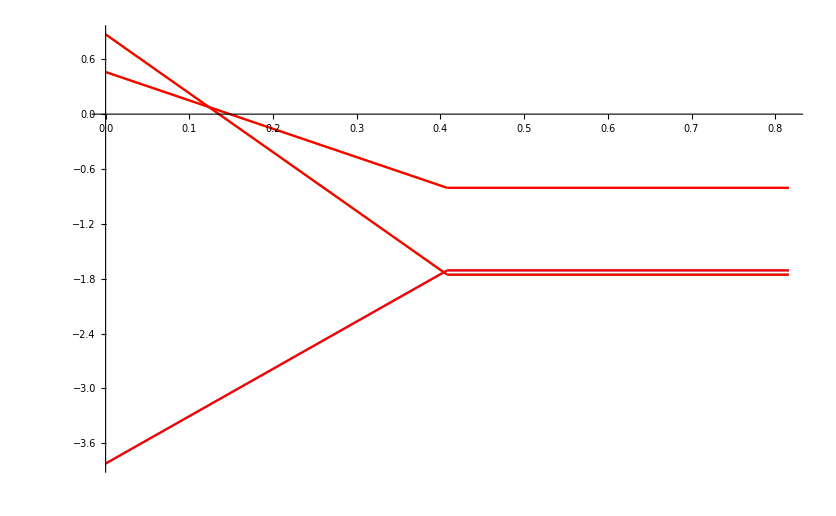

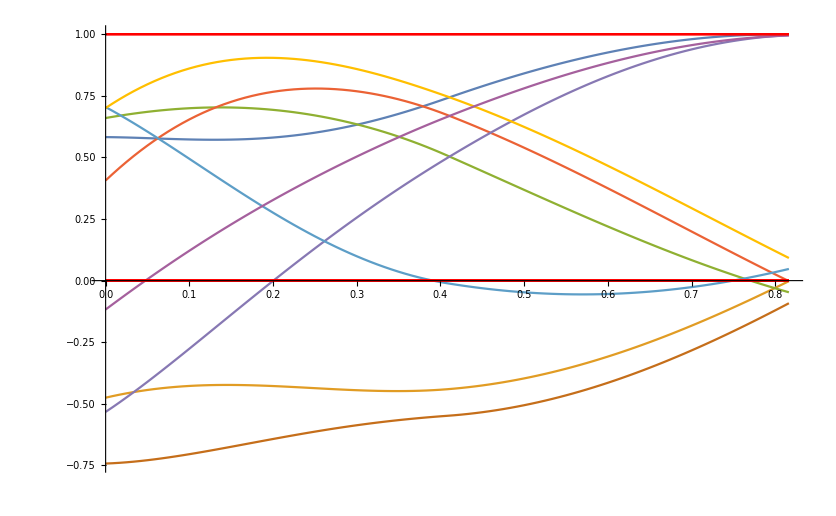

```mathematica
history = controller[ω0,ω1,θ0, θTarget,nsteps,Δt,τ,False];
θlast = history[[-1]]["θ"];
AngleBetween[θ0, θTarget]*180/π
AngleBetween[θlast, θTarget] *180/π
Show[
ListLinePlot[Transpose[#["ω"]& /@ history], DataRange->{0, T}],
Plot[Flatten[axis[A[t]]], {t, 0, T}, PlotStyle->Red], PlotRange->All
]

Show[
ListLinePlot[Transpose[Flatten[#["θ"]] & /@ history], DataRange->{0, T}],
Plot[Flatten[θTarget], {t, 0, T}, PlotStyle->Red]
]
```

```mathematica
octane = GraphicsComplex[MeshCoordinates@#,MeshCells[#,2]]&@ Import["C:\\Users\\sam\\Dropbox\\RLBot\\meshes\\octane_decimated.stl"];
```

```mathematica
frames = ParallelTable[
Rasterize[
Graphics3D[{
Antialiasing->True,
Gray,
Polygon[{{-1, -1, 0}, {1, -1, 0}, {1, 1, 0}, {-1, 1, 0}} * 250],
EdgeForm[],Orange,
GeometricTransformation[octane, {history[[i]]["θ"],  history[[i]]["pos"] + {0, 0, -15}}],
Line[#["pos"] & /@ history[[1;;i]]]
}, 
Boxed->False,
Lighting->"Neutral",
ViewPoint->{250, -250, 125}, 
PlotRange-> {{-600, 300}, {-250, 250}, {-50, 500}},
ImageSize->1200
]
],
{i,1,nsteps-1}
];
```

```mathematica
ListAnimate[frames]
```

```mathematica
θ0 = RandomRotation[];
c = {0, 0, 0};
w = {1, 0.5, 0.3};
b = RandomReal[{1, 3}, 3];
```

```mathematica
Manipulate[
Θ = EulerAnglesToMatrix[{θx, 0, 0}];
r = Θ.(b-c);
Graphics3D[{
Opacity[0.25],
Sphere[b, 0.25],
Parallelepiped[-(Transpose[Θ].w)/2, DiagonalMatrix[w].Θ],
Opacity[1],
Arrow[{c, #}]& /@ (0.5Θ),
Red,
Arrow[{c, b}],



Line[{c, #}]& /@ (DiagonalMatrix[r].Θ)
},
Boxed->False,
PlotRange->All],
{θx, 0, 1}
]
```